```mathematica
Table[ShowGraph5Least[k],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,
alfaKey,betaKey,gammaKey,deltaKey,epsilonKey}}]
```

{-Graphics-361660,-Graphics-317380,-Graphics-296080,-Graphics-361120,-Graphics-317140,-Graphics-359771,-Graphics-316811,-Graphics-230411,-Graphics-208031,-Graphics-272591}

```mathematica
allGraphs5[35977]
```

<|signature→35977,matrix→{{2,1,2,1,1},{1,2,1,0,0},{2,1,2,1,1},{1,0,1,2,1},{1,0,1,1,2}},graph→-Graphics-,vertexsets→{{1,3},{2},{4},{5}},vertices→{1,2,3,4},edges→{1<->2,1<->3,1<->4,3<->4},relations→{x35977==x36058+x36166,x35977==x36004+x36112,x35977==x35976-x35978,x35977==x35245-x36736,x35977==x35245-x36736,x35977==x33781-x38254,x35977==x33781-x38254,x35977==x22855-x29416,x35977==x22852-x29413,x35977==x22846-x29407,x35977==x22843-x29404,x35977==x22612-x29173,x35977==x22609-x29170,x35977==x22603-x29164,x35977==x22600-x29161,x35977==x22126-x28687,x35977==x22117-x28678,x35977==x21883-x28444,x35977==x21874-x28435,x35977==x20668-x27229,x35977==x20665-x27226,x35977==x20425-x26986,x35977==x20422-x26983,x35977==x19939-x26500,x35977==x19696-x26257,x35977==x16051-x56011,x35977==x16051-x56011,x35977==x3172-x9733,x35977==x3169-x9730,x35977==x3163-x9724,x35977==x3160-x9721,x35977==x2443-x9004,x35977==x2434-x8995,x35977==-x7546+x985,x35977==-x7543+x982,x35977==x256-x6817},links→{},parents→{35976,35245,35245,33781,33781,22855,22852,22846,22843,22612,22609,22603,22600,22126,22117,21883,21874,20668,20665,20425,20422,19939,19696,16051,16051,3172,3169,3163,3160,2443,2434,985,982,256},children→{{36058,36166},{36004,36112}},comp→Greater,compwhy→This is a planar contraction,colofour→v13x24x5+v13x25x4+v13x2x4x5,colortable→{{0,v13x24x5+v13x25x4+v13x2x4x5},{v13x24x5+v13x25x4+v13x2x4x5,0},{0,v13x24x5+v13x25x4+v13x2x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5},{v13x24x5,v13x25x4+v13x2x4x5},{v13x25x4,v13x24x5+v13x2x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5}},colofournull→1/12 (-p12345-p1234x5-p1235x4-5 p123x45+2 p123x4x5+p1245x3+p124x35+p125x34+p12x345+4 p12x3x45-2 p12x3x4x5-3 p1345x2+p134x25-2 p134x2x5+p135x24-2 p135x2x4+p13x245-4 p13x2x45+2 p13x2x4x5+p145x23+2 p145x2x3+p14x235-2 p14x25x3+2 p14x2x35+p15x234-2 p15x24x3+2 p15x2x34+p1x2345+4 p1x23x45-2 p1x23x4x5-2 p1x245x3-2 p1x24x35+2 p1x24x3x5-2 p1x25x34+2 p1x25x3x4+2 p1x2x345-2 p1x2x3x45),colofourrealnull→-2 n12345+n1234x5+n1235x4+n123x45-n123x4x5+2 n1345x2-n134x2x5-n135x2x4-n13x2x45+n13x2x4x5,atleast→1,atleastwhy→Comp is 'greater'.,embed→1/24 ChromaticPolynomial[EdgeAdd[EdgeAdd[EdgeAdd[EdgeAdd[EdgeAdd[EdgeAdd[VertexContract[EdgeDelete[VertexDelete[Graph[$Failed⟦8⟧],14],{7<->13,13<->12,12<->17,17<->15,15<->7}],{12,7}],{12<->13}],{12<->15}],{12<->17}],{13<->15}],{13<->17}],{15<->17}],4]+1/24 ChromaticPolynomial[EdgeAdd[EdgeAdd[EdgeAdd[VertexContract[VertexContract[EdgeDelete[VertexDelete[Graph[$Failed⟦8⟧],14],{7<->13,13<->12,12<->17,17<->15,15<->7}],{12,7}],{13,15}],{12<->13}],{12<->17}],{13<->17}],4]+1/24 ChromaticPolynomial[EdgeAdd[EdgeAdd[EdgeAdd[VertexContract[VertexContract[EdgeDelete[VertexDelete[Graph[$Failed⟦8⟧],14],{7<->13,13<->12,12<->17,17<->15,15<->7}],{12,7}],{13,17}],{12<->13}],{12<->15}],{13<->15}],4],colofourgenerator→g13x24x5+g13x25x4-g13x2x4x5-g1x24x3x5-g1x25x3x4+g1x2x3x4x5,colotree→2 t1345x2-t134x25-t134x2x5-t135x24-t135x2x4+t13x24x5+t13x2x4x5|>

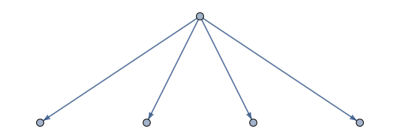

```mathematica
35977->{{36058,36166},{36004,36112}}//Gr
```

```mathematica
Gr[l_]:=Block[{g=Graph[{},{}], v={}, head, tail},
head=l[[1]];
tail=l[[2]];
Table[g=EdgeAdd[g,head->node],{node,Flatten[tail]}];
g
];
```

```mathematica
RecursiveChildren[n_]:=Flatten[allGraphs5[n,"children"]]
```

```mathematica
RecursiveChildren[lambdaKey]
```

{27226,35977,22852,31681,20746,23041,20692,20803,20668,27259}

```mathematica
Traverse[n_]:=Block[{g=Graph[{},{}], v={}, head, tail, todo, done, children, current, vertices={},from,to,edgeColors={},edge,vertexColors={}, vertexShapes={},delete={},fromg,tog, styles, style},
todo={n};
done={};
While[todo!={},
current=First[todo];
from=ToString[allGraphs5[current,"comp"]];
AppendTo[vertexColors,current->If[from=="Greater",Darker[Green],If[from=="GreaterEqual",Orange,Red]]];
g=VertexAdd[g,current];
fromg=allGraphs5[current,"graph"];
AppendTo[vertexShapes,current->If[VertexCount[fromg]==5,"Pentagon",If[VertexCount[fromg]==4,"Square","Triangle"]]];
AppendTo[vertices,current->ShowGraph5Least[current]];
todo= Rest[todo];
If[!MemberQ[done,current],
AppendTo[done,current];
children=allGraphs5[current,"children"];
styles=Join[{Dotted,DotDashed, Dashed},Table[Dashing[r],{r,Table[00+0.02*k,{k,0,10}]}]];
Table[
style=First[styles];
styles=Rest[styles];
Table[
to=ToString[allGraphs5[child,"comp"]];
tog=allGraphs5[child,"graph"];
edge=DirectedEdge[current,child];
If[VertexCount[fromg]==5&&EdgeCount[fromg]==6&&VertexCount[tog]==4&&EdgeCount[tog]==5,AppendTo[delete,edge]];
g=EdgeAdd[g,edge];
AppendTo[edgeColors,edge->Directive[Thickness[0.005],style,If[from=="Greater",If[to=="Greater",Darker[Green],Orange],If[to=="GreaterOrEqual",Orange,Red]]]],
{child,childPair}]
,{childPair,children}];
todo=Join[todo,Flatten[ children]]
];
];
Graph[Reverse[VertexList[g]],Reverse[EdgeList[g]], VertexLabels->vertices, ImageSize->800, DirectedEdges->True, EdgeStyle->edgeColors, VertexStyle->vertexColors, VertexShapeFunction->vertexShapes]
]
```

```mathematica
SelectFirst[{{"Greater","Equal"}}]
```

```mathematica
IntegerDigits[22852,3]//Total
```

6

```mathematica
allGraphs5[lambdaKey,"comp"]//ToString
```

Greater

```mathematica
IntegerDigits[20668,3]
```

{1,0,0,1,1,0,0,1,1,1}

```mathematica
alfa1Key
```

36166

```mathematica
alfaKey
```

35977

```mathematica
amigos
```

{29413,20773,27229,22933,20695}

```mathematica
IntegerDigits[27226,3]
```

{1,1,0,1,1,0,0,1,0,1}

```mathematica
toDelete={27226->29602,27226->27364,22852->22990,22852->29446,20746->36058,20746->27340,20692->36004,20692->31708,20668->31684,20668->23044}
```

{27226->29602,27226->27364,22852->22990,22852->29446,20746->36058,20746->27340,20692->36004,20692->31708,20668->31684,20668->23044}

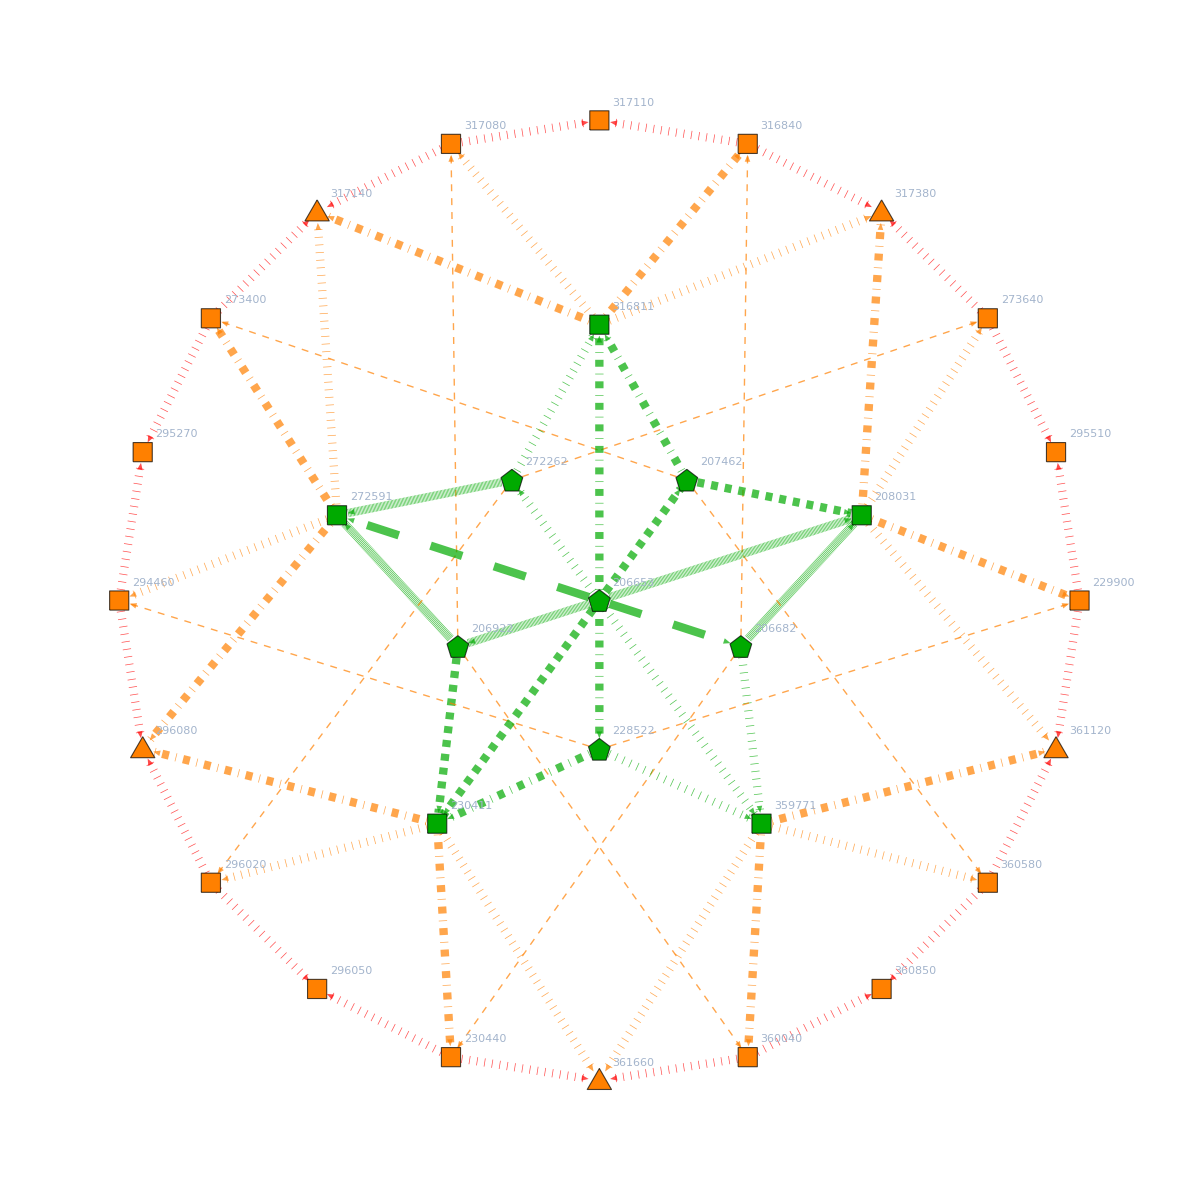

```mathematica
With[{h=Graph[EdgeDelete[VertexDelete[Traverse[lambdaKey],Select[VertexList[Traverse[lambdaKey]],With[{g=allGraphs5[#,"graph"]},(VertexCount[g]==5&&EdgeCount[g]>=7)]&]],
toDelete], GraphLayout->"TutteEmbedding", ImageSize->1200]},
Graph[VertexDelete[Traverse[lambdaKey],Select[VertexList[Traverse[lambdaKey]],With[{g=allGraphs5[#,"graph"]},(VertexCount[g]==5&&EdgeCount[g]>=7)]&]], VertexCoordinates->GraphEmbedding[h], ImageSize->1200,EdgeStyle->Map[#->Directive[Orange,Dashed,Thick]&,toDelete]]]
```

```mathematica
Map[IntegerDigits[#,3]&,{22852,29446}]
```

{{1,0,1,1,1,0,0,1,0,1},{1,1,1,1,1,0,1,1,2,1}}

```mathematica
Map[ShowGraph5Least,{22852,29446}]
```

{-Graphics-228522,-Graphics-294460}

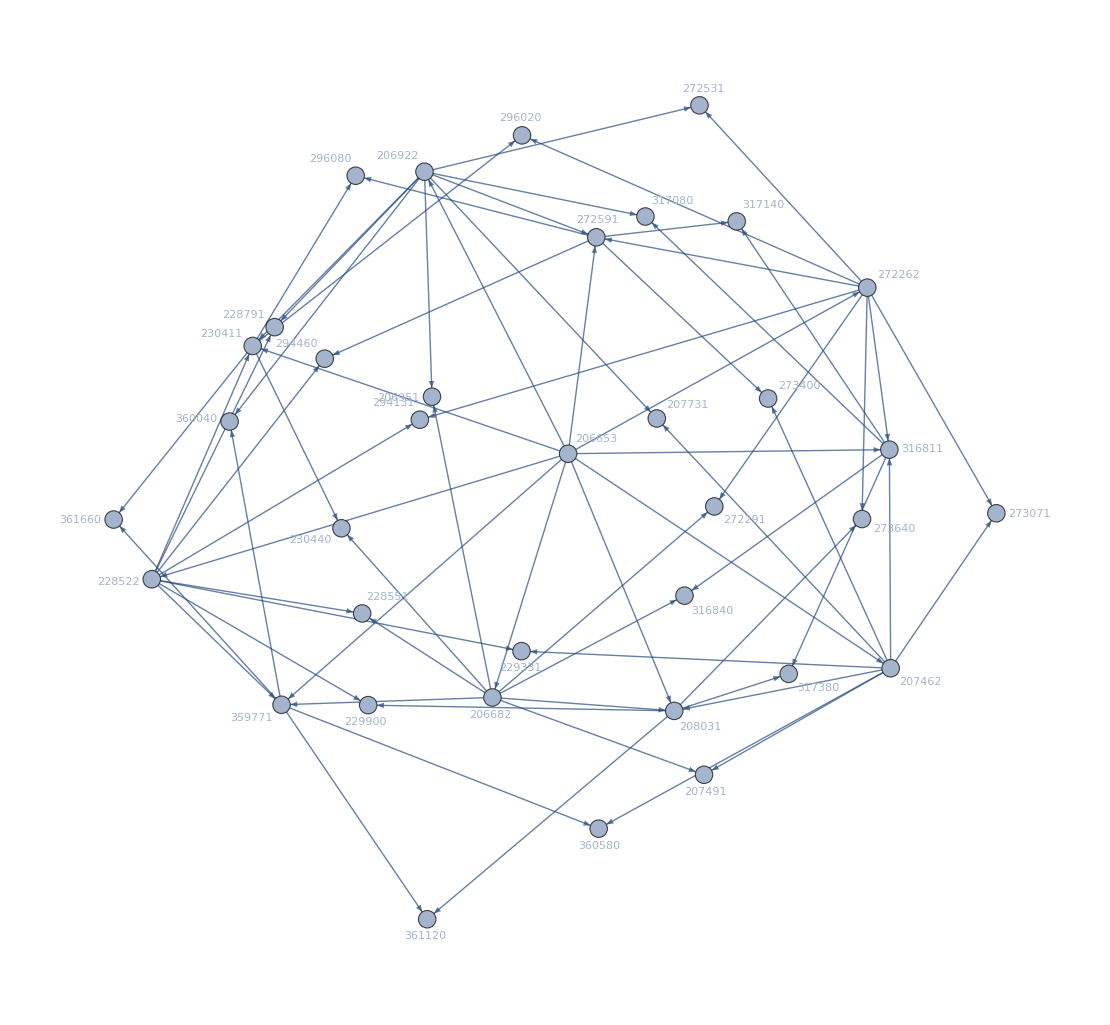

```mathematica
With[{g=Graph[Flatten[Table[EdgeList[Gr[k->allGraphs5[k,"children"]]],{k,Join[{lambdaKey},RecursiveChildren[lambdaKey]]}]], GraphLayout->"LayeredDigraphEmbedding"]},
Graph[VertexList[g],EdgeList[g],VertexLabels->Map[#->ShowGraph5Least[#]&,VertexList[g]], GraphLayout->"SpringEmbedding"]]
```

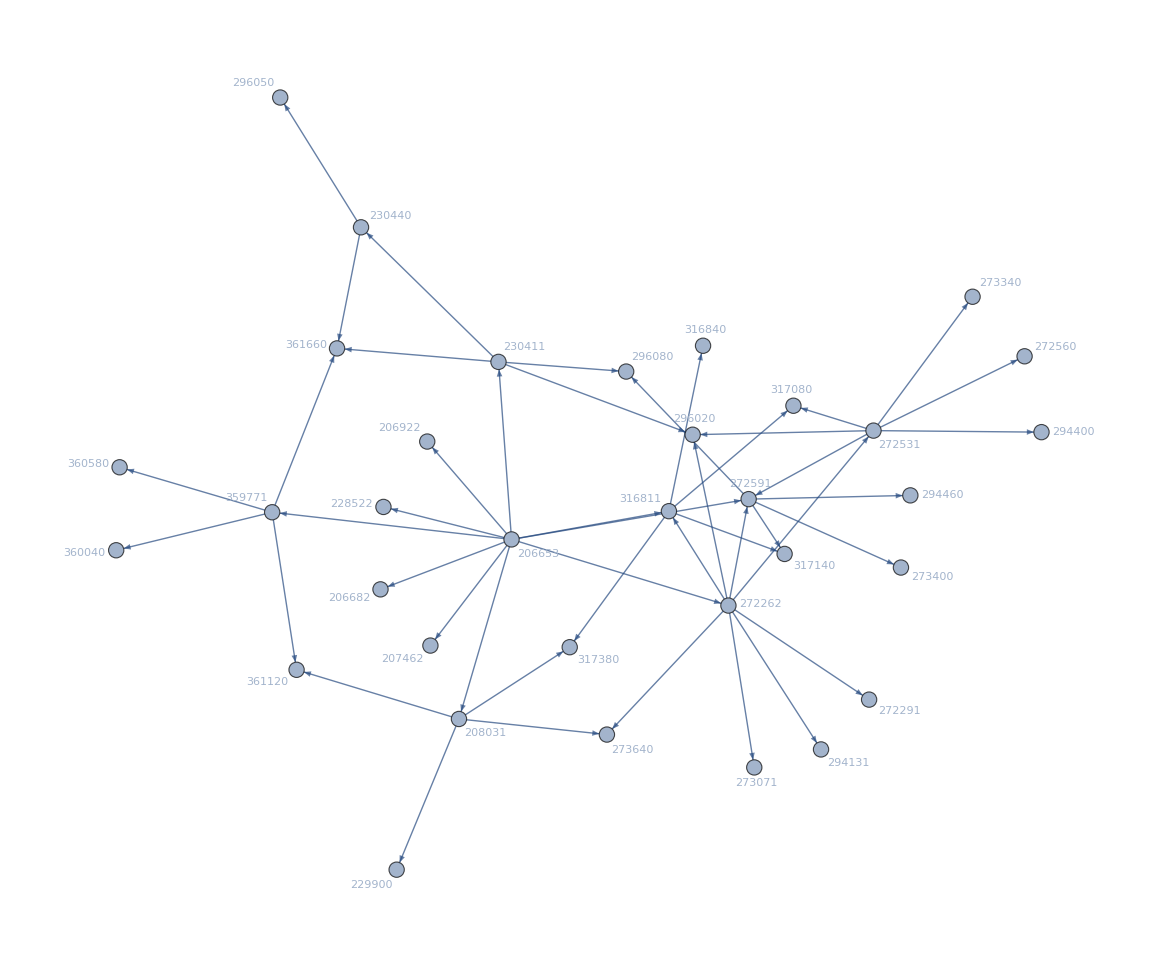

```mathematica
With[{g=Graph[Flatten[Table[EdgeList[Gr[k->allGraphs5[k,"children"]]],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,
alfaKey,betaKey,gammaKey,deltaKey,epsilonKey, lambdaKey,
27226,23044,
27253}}]], GraphLayout->"LayeredDigraphEmbedding"]},
Graph[VertexList[g],EdgeList[g],VertexLabels->Map[#->ShowGraph5Least[#]&,VertexList[g]], GraphLayout->"SpringElectricalEmbedding"]]
```

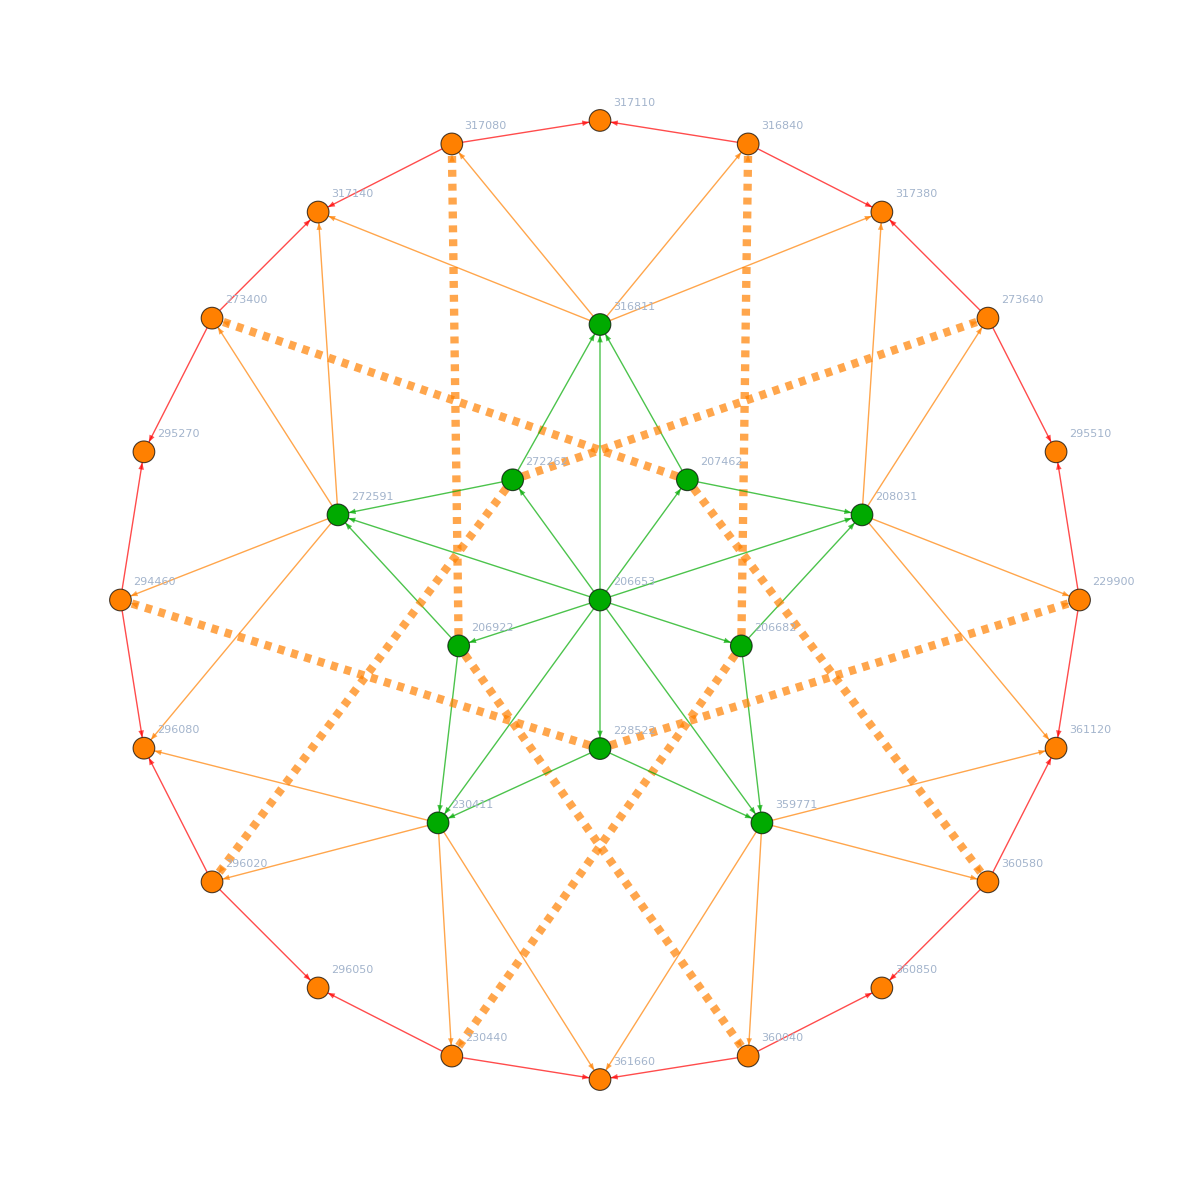

```mathematica
With[{h=Graph[EdgeDelete[VertexDelete[Traverse[lambdaKey],Select[VertexList[Traverse[lambdaKey]],With[{g=allGraphs5[#,"graph"]},(VertexCount[g]==5&&EdgeCount[g]>=7)]&]],
toDelete], GraphLayout->"TutteEmbedding", ImageSize->1200]},
Graph[VertexDelete[Traverse[lambdaKey],Select[VertexList[Traverse[lambdaKey]],With[{g=allGraphs5[#,"graph"]},(VertexCount[g]==5&&EdgeCount[g]>=7)]&]], VertexCoordinates->GraphEmbedding[h], ImageSize->1200,EdgeStyle->Map[#->Directive[Thickness[0.005],Orange,Dashed]&,toDelete]]]
```